```mathematica
NS["infinite_N2","C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"];
```

```mathematica
h[x_]=-x*Log[x]-(1-x)*Log[1-x];
```

```mathematica
lpd[x_,j1_,j2_,j3_:0,j4_:0]=h[x]+j1*x+j2*x^2+j3*x^3+j4*x^4;
```

```mathematica
sj={-29559.0871554411198283397`12.,380136.7678181689272976126`12.,-4.1511764356194754842594129`12.*^6,-327746.6081515182486243527`12.};
```

```mathematica
FS@D[lpd[x,j1,j2],{x,1}]
```

j1+2 j2 x+2 ArcTanh[1-2 x]

```mathematica
Reduce[%==0,{j1,j2}]
```

(x==0&&j1==-∞)||(x≠0&&j2==(-j1-2 ArcTanh[1-2 x])/(2 x))

```mathematica
j2c[j1_,x_]=(-j1-2 ArcTanh[1-2 x])/(2 x);
```

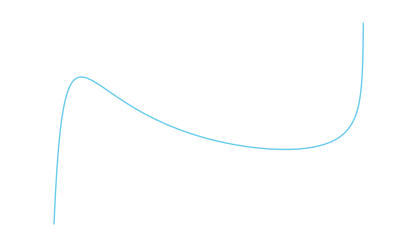

```mathematica
Plot[j2c[-3,x],{x,0,1},Axes->None]
```

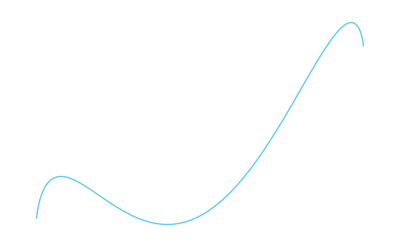

```mathematica
Plot[lpd[x,-3,j2c[-3,0.4]],{x,0,1},PlotRange->All]
```

```mathematica
(* Study of the infinite N limit *)
```

```mathematica
assu=(Element[m,Reals]&&Element[v,Reals]&&Element[p,Reals]&&k>2);
assup=(Element[m,Reals]&&v>0&&p>0&&k>2);
assun=(Element[m,Reals]&&v<0&&p<0&&k>2);
```

```mathematica
z[m_,p_]=Assuming[assu,FS@Integrate[Exp[-(m-x)^2*p/2],{x,0,1},Assumptions->assu]]
```

(√(π/2) (-Erf[((-1+m) √p)/(√2)]+Erf[(m √p)/(√2)]))/(√p)

```mathematica
pd[x_,m_,p_]=Assuming[assu,FS@Exp[-(m-x)^2*p/2]/z[m,p]]
```

(ⅇ^(-1/2 p (m-x)^2) √p √(2/π))/(-Erf[((-1+m) √p)/(√2)]+Erf[(m √p)/(√2)])

```mathematica
pd[x_,m_,0]=Limit[pd[x,m,p],p->0]
```

1

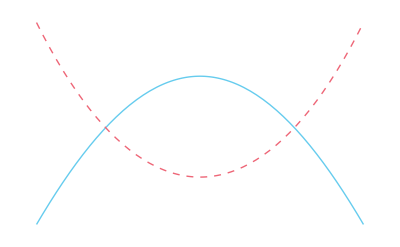

```mathematica
Plot[{pd[x,0.5,1],pd[x,0.5,-1]},{x,0,1},ImageSize->a4shortside]
```

```mathematica
mom[n_,m_,p_]:=Assuming[assu,FS[Integrate[x^n*pd[x,m,p],{x,0,1},Assumptions->assu]]]
```

```mathematica
mom[1,0.5,1]
```

0.5

```mathematica
mom[1,0.5,-3]
```

0.5

```mathematica
Assuming[assu,FS@D[z[m,p],m]]
```

ⅇ^(-1/2 (1+m^2) p) (ⅇ^(p/2)-ⅇ^(m p))

```mathematica
mom[1,m,p]*z[m,p]
```

ConditionalExpression[(√(π/2) (m+(ⅇ^(-1/2 (1+m^2) p) (-ⅇ^(p/2)+ⅇ^(m p)) √(2/π))/(√p (Erf[((-1+m) √p)/(√2)]-Erf[(m √p)/(√2)]))) (-Erf[((-1+m) √p)/(√2)]+Erf[(m √p)/(√2)]))/(√p),p>0]

```mathematica
Limit[Binomial[n*x,6]/Binomial[n,6],n->+Infinity]
```

x^6

```mathematica
z2[m_,p_]=Assuming[assu,FS@Integrate[Exp[m*x+p*x^2],{x,0,1},Assumptions->assu]]
```

(-DawsonF[m/(2 √p)]+ⅇ^(m+p) DawsonF[(m+2 p)/(2 √p)])/(√p)

```mathematica
pd2[x_,m_,p_]=Assuming[assu,FS[Exp[m*x+p*x^2]/z2[m,p]]]
```

-(ⅇ^(x (m+p x)) √p)/(DawsonF[m/(2 √p)]-ⅇ^(m+p) DawsonF[(m+2 p)/(2 √p)])

```mathematica
pd2[x_,m_,0]=Limit[pd2[x,m,p],p->0]
```

$Aborted

```mathematica
Assuming[assu,FS[D[z2[m,p],m]==Integrate[x*Exp[m*x+p*x^2],{x,0,1}]]]
```

True

```mathematica
Assuming[assu,FS@Integrate[Exp[m*(x-x1)+p*(x^2-x2)],{x,0,1},Assumptions->assu]]
```

(ⅇ^(-m x1-p x2) (-DawsonF[m/(2 √p)]+ⅇ^(m+p) DawsonF[(m+2 p)/(2 √p)]))/(√p)

```mathematica
Assuming[assu,FS[Log[z2[m,p]]]]
```

Log[(-DawsonF[m/(2 √p)]+ⅇ^(m+p) DawsonF[(m+2 p)/(2 √p)])/(√p)]

```mathematica
(* load first four raw moments from Stensola data (3 ms) *)
n=65;means=Flatten@Import["norm_binomeans.csv"][[2;;]]
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

```mathematica
{aa1,aa2,aa3,aa4}=means;
```

```mathematica
MEhomsolutioninf[meanmm_,meancorr_,wp_:MachinePrecision]:=Block[{totcorr=meancorr,totmm=meanmm,totalprob,js2,js1,freeenm,varm,soluzm,prob,bvalues},
freeenm[js1_,js2_]:=
-js1*totmm-js2*totcorr+Log[Integrate[Exp[js1*x+js2*x^2],{x,0,1}]](*(-DawsonF[js1/(2*Sqrt[js2])]+Exp[js1+js2]*DawsonF[(js1+2*js2)/(2*Sqrt[js2])])/Sqrt[js2]]*)
;
soluzm=NMinimize[freeenm[js1,js2],{js1,js2},MaxIterations->10000,PrecisionGoal->6,Method->Automatic,AccuracyGoal->Infinity,WorkingPrecision->wp];
{js1/.soluzm[[2]],js2/.soluzm[[2]]}]
```

```mathematica
solu=MEhomsolutioninf[aa1,aa2,12]
```

{86.8025475443,-4804.10917772}

```mathematica
Integrate[{x,x^2}*pd2[x,Sequence@@solu],{x,0,1}]
```

{0.01242038,0.0002162858}

```mathematica
means
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

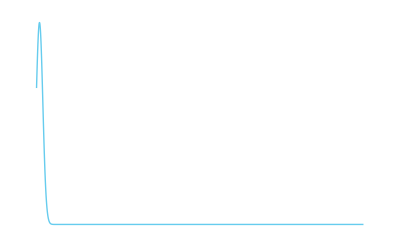

```mathematica
Plot[pd2[x,Sequence@@solu],{x,0,1},PlotRange->All,ImageSize->a4shortside]
```

```mathematica
MEhomsolutioninf4[mean1_,mean2_,mean3_,mean4_,wp_:MachinePrecision]:=Block[{totalprob,js1,js2,js3,js4,freeenm,varm,soluzm,prob,bvalues},
freeenm[js1_,js2_,js3_,js4_]:=
-js1*mean1-js2*mean2-js3*mean3-js4*mean4+Log[NIntegrate[Exp[js1*x+js2*x^2+js3*x^3+js4*x^4],{x,0,1},PrecisionGoal->6,AccuracyGoal->Infinity,WorkingPrecision->wp]](*(-DawsonF[js1/(2*Sqrt[js2])]+Exp[js1+js2]*DawsonF[(js1+2*js2)/(2*Sqrt[js2])])/Sqrt[js2]]*)
;
soluzm=NMinimize[freeenm[js1,js2,js3,js4],{js1,js2,js3,js4},MaxIterations->10000,PrecisionGoal->6,Method->Automatic,AccuracyGoal->Infinity,WorkingPrecision->wp]
(*{js1,js2,js3,js4}/.soluzm[[2]]*)]
```

```mathematica
solu=MEhomsolutioninf4[aa1,aa2,aa3,aa4,24]
```

{-3.52091959779814756004157,{js1→81.6017249745994883034575,js2→-4417.30338427256902871301,js3→-7524.3373393306105447331,js4→-1080.03805042180495269952}}

```mathematica
Integrate[{x,x^2,x^3,x^4}*pd2[x,Sequence@@solu],{x,0,1}]
```

{0.01242038,0.0002162858}

```mathematica
Plot[pd2[x,Sequence@@solu],{x,0,1},PlotRange->All,ImageSize->a4shortside]
```

-Graphics-

```mathematica
Assuming[0<x<1,FS@Series[Binomial[nx,nx*x],{nx,Infinity,1},Assumptions->0<x<1]]
```

ⅇ^(((-1+x) Log[1-x]-x Log[x]) nx+O[1/nx]^2) ((√(1/nx))/(√(2 π) √(-(-1+x) x))+O[1/nx]^(3/2))

```mathematica
h[x_]=-x*Log[x]-(1-x)*Log[1-x];
```

```mathematica
lpd[x_,j1_,j2_,j3_:0,j4_:0]=h[x]+j1*x+j2*x^2+j3*x^3+j4*x^4;
```

```mathematica
sj={-29559.0871554411198283397`12.,380136.7678181689272976126`12.,-4.1511764356194754842594129`12.*^6,-327746.6081515182486243527`12.};
```

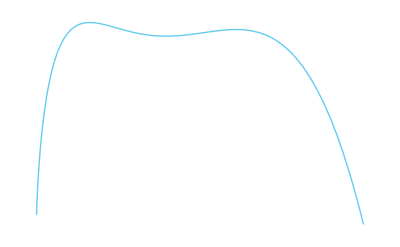

```mathematica
Plot[lpd[x,Sequence@@(sj/5000)],{x,0,0.04},ImageSize->a4shortside,PlotRange->Auto]
```

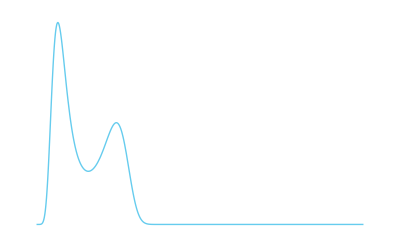

```mathematica
Plot[Exp[5000*lpd[x,Sequence@@(sj/5000)]],{x,0,0.1},ImageSize->a4shortside,PlotRange->All]
```

```mathematica
NIntegrate[Exp[5000*lpd[x,Sequence@@(sj/5000)]],{x,0,1}]
```

1.91424×10^6

```mathematica
Integrate[Exp[-n*k*(x-a)^2/2],{x,0,1},Assumptions->(n>1&&0<a<1)]
```

(√(π/2) (-Erf[((-1+a) √(k n))/(√2)]+Erf[(a √(k n))/(√2)]))/(√(k n))

```mathematica
FS[Log[%]]
```

Log[(√(π/2) (-Erf[((-1+a) √(k n))/(√2)]+Erf[(a √(k n))/(√2)]))/(√(k n))]

```mathematica
Series[%37,{n,+Infinity,0},Assumptions->(k>0&&0<a<1)]
```

((√(2 π) √(1/n))/(√k)+O[1/n]^(5/2))+ⅇ^((-k/2+a k-(a^2 k)/2) n+O[1/n]^5) (1/((-1+a) k n)-1/((-1+a)^3 k^2 n^2)+O[1/n]^3)+ⅇ^(-1/2 (a^2 k) n+O[1/n]^4) (-1/(a k n)+1/(a^3 k^2 n^2)+O[1/n]^3)

```mathematica
Series[%37,{n,+Infinity,0},Assumptions->(k<0&&0<a<1)]
```

$Aborted

```mathematica
<<"ME_homsolution.m";
```

```mathematica
(* load first four raw moments from Stensola data (3 ms) *)

n=65;means=Flatten@Import["norm_binomeans.csv"][[2;;]]
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

```mathematica
{aa1,aa2,aa3,aa4}=means;
```

```mathematica
nn=5000;rann=Range[0,nn];
```

```mathematica
(* find Lagr multipliers, 2 constraints.
MEhomsolution usually give better-precision results than MEhomsolution2 *)
{zj1,zj2,qpop,norm2}=MEhomsolution[aa1,aa2,nn,12];
```

```mathematica
{zj1,zj2}/nn
```

{-4.49217265967,4.49019290816}

```mathematica
{ij1,ij2,totprob}=MEhomsolutioni[aa1,aa2,nn,12]
```

{-4.5015248404,4.50037384375,7.54453200775×10^22}

```mathematica
{ij1,ij2,totprob}=MEhomsolutioni[aa1,aa2,10000,60]
```

$Aborted

```mathematica
(* find Lagr multipliers, 2 constraints *)
{zj1,zj2,qq2ex,norm2}=MEhomsolution2[aa1,aa2,nn,12];
```

```mathematica
{zj1,zj2}
```

{-22449.2940092,22429.6391226}

```mathematica
{{"measured",aa1,aa2,aa3,aa4},Prepend["predicted"]@Table[(Binomial[rann,i].MEhomprob[zj1,zj2,nn])/Binomial[nn,i],{i,4}]}//T//MF//N
```

(measured | predicted
0.0124204 | 0.0124197
0.000216286 | 0.000215596
4.59777×10^-6 | 0.0000637286
1.07013×10^-7 | 0.0000610869)